```mathematica
Metodo de Newton
```

```mathematica
newt [ec_,x0_]:=(
length = 5;
arr=Table[z,length];
linep=Table[z,length];
tan=Table[z,length];
d =D[ec,x];
potence = ec[[-1]][[-1]];
If[potence >2, dc=D[ec,{x,(potence-2)}],
dc =D[ec,x]
];
arr[[1]]={x0,ReplaceAll[ec,x->x0]};
linep[[1]]=ListLinePlot[{arr[[1]],{x0,0}},PlotStyle->{{Green,Dashed}}];
tan[[1]]=ListLinePlot[{arr[[1]]},PlotStyle->{{Red}}];
Print[arr[[1]]];
For[i=2,i<=length,i++,(
xi=arr[[i-1]][[1]];
xi2=arr[[i-1]][[2]];
xn =N[xi-(ReplaceAll[ec,x->xi]/ReplaceAll[d,x->xi]),6];
arr[[i]]={xn, N[ReplaceAll[ec,x->xn],6]};
linep[[i]]=ListLinePlot[{arr[[i]],{xn,0}},PlotStyle->{{Green,Dashed}}];
tan[[i]]=ListLinePlot[{{xi,xi2},{xn,0}},PlotStyle->{{Red}}];
Print[arr[[i]]];
)];
p2= Plot[{ec},{x,-(x0+2),x0+2},Epilog->{Black,AbsolutePointSize[5],Point[arr]}];
Show[p2,linep,tan]
)
```

{5,2994}

{4.01804,977.41}

{3.2385,318.}

{2.624,102.7}

{2.147,32.6}

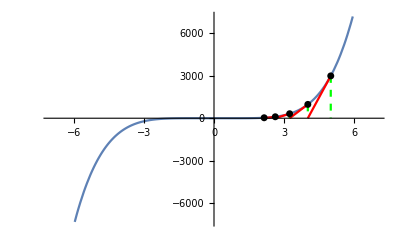

```mathematica
newt[x^5-x^3-x-1,5]
```